```mathematica
description="Leading order cross section of slepton pair production.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"(*, "FormCalc"*)};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
(*Install["LoopTools"];
Install["bca"];*)
```

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[p3, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(3\)]\)"; 
MakeBoxes[p4, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(4\)]\)";
```

## Self-energies

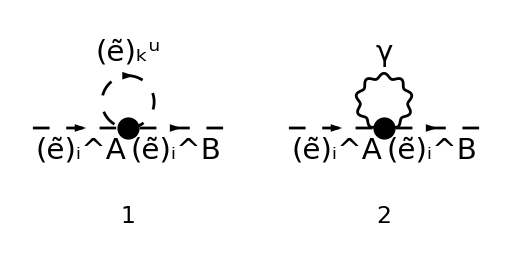

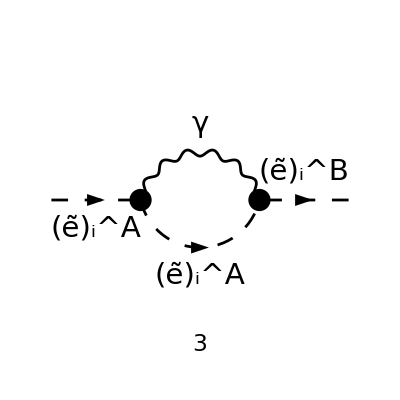

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,1->1,ExcludeTopologies->{Tadpoles}],
{S[12,{A,i}]}->{S[12,{B,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],S[5],S[6],V[2],V[3],F[11],F[12],S[13],S[14],S[11]}
];
Paint[
diags[0],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

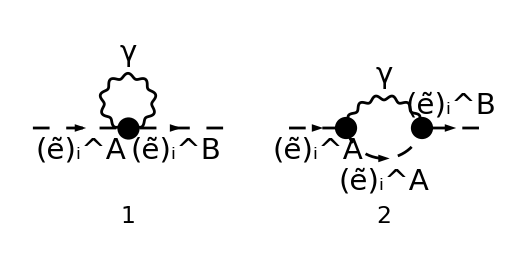

```mathematica
diags[1]=DiagramExtract[diags[0],{2,3}];
Paint[
diags[1],
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p},
OutgoingMomenta->{p},
LoopMomenta->{kloop},
ChangeDimension->D,
UndoChiralSplittings->True,
(*LorentzIndexNames->{μ,ν},*)
Contract->True,
DropSumOver->True,
SMP->True,
List->True
]
```

{-(ⅈ D e^2 IndexDelta(A,B))/(16 π^4 kloop^2),-(ⅈ e^2 (-2 (kloop·p)-kloop^2-p^2) IndexDelta(A,B))/(16 π^4 (kloop^2-(MSf(A,2,i))^2).(kloop-p)^2)}

#### Diagram with single (4-point) vertex

```mathematica
M1[0]=Mlist[0][[1]]
```

-(ⅈ D e^2 IndexDelta(A,B))/(16 π^4 kloop^2)

```mathematica
M1[1]=M1[0]//TID[#,kloop]&
```

0

#### Diagram with two (3-point) vertices

```mathematica
M2[0]=Mlist[0][[2]]
```

-(ⅈ e^2 (-2 (kloop·p)-kloop^2-p^2) IndexDelta(A,B))/(16 π^4 (kloop^2-(MSf(A,2,i))^2).(kloop-p)^2)

```mathematica
M2[1]=M2[0]//TID[#,kloop,ToPaVe->True]&
```

(e^2 IndexDelta(A,B) A_0((MSf(A,2,i))^2))/(16 π^2)-(e^2 IndexDelta(A,B) ((MSf(A,2,i))^2+p^2) B_0(p^2,0,(MSf(A,2,i))^2))/(8 π^2)

```mathematica
M2[0]/.{MSf[A,2,i]->m}//Simplify
M2[1]/.{MSf[A,2,i]->m}//Simplify
```

(ⅈ e^2 (2 (kloop·p)+kloop^2+p^2) IndexDelta(A,B))/(16 π^4 (kloop^2-m^2).(kloop-p)^2)

(e^2 IndexDelta(A,B) (A_0(m^2)-2 (m^2+p^2) B_0(p^2,0,m^2)))/(16 π^2)

## Full diagrams with slepton self-energies

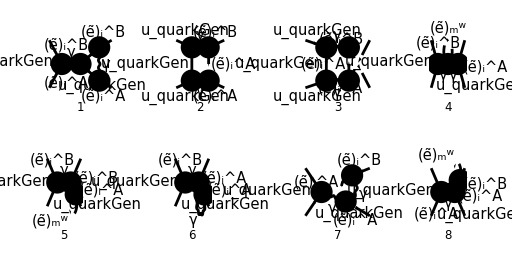

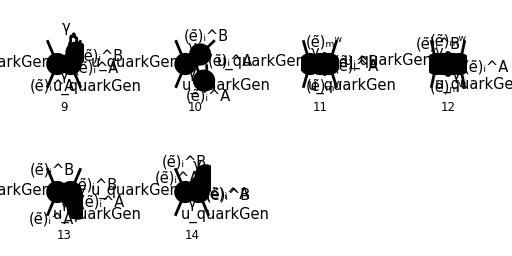

```mathematica
diagsFull[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],S[5],S[6],V[2],V[3],F[11],F[12],S[13],S[14],S[11]},
LastSelections->{V[1],S[12]}
];
Paint[
diagsFull[0],
ColumnsXRows->{4,2},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

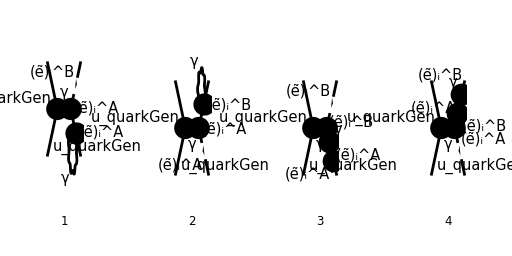

```mathematica
diagsFull[1]=DiagramExtract[diagsFull[0],{6,9,13,14}];
Paint[
diagsFull[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diagsFull[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{kloop},
ChangeDimension->D,
UndoChiralSplittings->True,
Contract->True,
DropSumOver->True,
SMP->True,
List->True
]/.{MQU[QuarkGen]->0}
```

{-(ⅈ D e^4 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k2-k1)).(φ(p_1,MQU(quarkGen))))/(24 π^4 kloop^2 (k1+k2)^2 (k2^2-(MSf(A,2,i))^2)),(ⅈ D e^4 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k1-k2)).(φ(p_1,MQU(quarkGen))))/(24 π^4 kloop^2 (k1+k2)^2 (k1^2-(MSf(A,2,i))^2)),-((ⅈ e^4 δ_Col1Col2 (2 (k2·kloop)-k2^2-kloop^2) IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k2-k1)).(φ(p_1,MQU(quarkGen))))/(24 π^4 (k1+k2)^2 (k2^2-(MSf(B,2,i))^2) (kloop^2-(MSf(A,2,i))^2).(k2+kloop)^2)),(ⅈ e^4 δ_Col1Col2 (2 (k1·kloop)-k1^2-kloop^2) IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k1-k2)).(φ(p_1,MQU(quarkGen))))/(24 π^4 (k1+k2)^2 (k1^2-(MSf(A,2,i))^2) (kloop^2-(MSf(B,2,i))^2).(k1+kloop)^2)}

### Check that the “flower”-diagrams still give zero

```mathematica
Mflower[0]=Total[Mlist[0][[{1,2}]]]
```

(ⅈ D e^4 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k1-k2)).(φ(p_1,MQU(quarkGen))))/(24 π^4 kloop^2 (k1+k2)^2 (k1^2-(MSf(A,2,i))^2))-(ⅈ D e^4 δ_Col1Col2 IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k2-k1)).(φ(p_1,MQU(quarkGen))))/(24 π^4 kloop^2 (k1+k2)^2 (k2^2-(MSf(A,2,i))^2))

```mathematica
Mflower[1]=Mflower[0]//TID[#,kloop,ToPaVe->True]&
```

0

### Do the bubble diagrams

```mathematica
Mbubble[0]=Total[Mlist[0][[{3,4}]]]
```

(ⅈ e^4 δ_Col1Col2 (2 (k1·kloop)-k1^2-kloop^2) IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k1-k2)).(φ(p_1,MQU(quarkGen))))/(24 π^4 (k1+k2)^2 (k1^2-(MSf(A,2,i))^2) (kloop^2-(MSf(B,2,i))^2).(k1+kloop)^2)-(ⅈ e^4 δ_Col1Col2 (2 (k2·kloop)-k2^2-kloop^2) IndexDelta(A,B) (φ(-p_2,MQU(quarkGen))).(γ·(k2-k1)).(φ(p_1,MQU(quarkGen))))/(24 π^4 (k1+k2)^2 (k2^2-(MSf(B,2,i))^2) (kloop^2-(MSf(A,2,i))^2).(k2+kloop)^2)

```mathematica
Mbubble[1]=Mbubble[0]//TID[#,kloop,ToPaVe->True]&//Simplify
```

-1/(24 π^2)e^4 δ_Col1Col2 IndexDelta(A,B) ((φ(-p_2,MQU(quarkGen))).(γ·k1).(φ(p_1,MQU(quarkGen)))-(φ(-p_2,MQU(quarkGen))).(γ·k2).(φ(p_1,MQU(quarkGen)))) ((A_0((MSf(B,2,i))^2))/((k1^2-(MSf(A,2,i))^2).(k1+k2)^2)+(A_0((MSf(A,2,i))^2))/((k2^2-(MSf(B,2,i))^2).(k1+k2)^2)-2 ((((MSf(B,2,i))^2+k1^2) B_0(k1^2,0,(MSf(B,2,i))^2))/((k1^2-(MSf(A,2,i))^2).(k1+k2)^2)+(((MSf(A,2,i))^2+k2^2) B_0(k2^2,0,(MSf(A,2,i))^2))/((k2^2-(MSf(B,2,i))^2).(k1+k2)^2)))